# Práctica 4. Sucesiones.

Así se introduce una sucesión:

```mathematica
a[n_]:=( (n+1)/n)^n
```

```mathematica
a[20]
```

21/20

Así se representa en forma de tabla y de matriz:

```mathematica
Table[a[n], {n, 1, 20}]
```

{2,9/4,64/27,625/256,7776/3125,117649/46656,2097152/823543,43046721/16777216,1000000000/387420489,25937424601/10000000000,743008370688/285311670611,23298085122481/8916100448256,793714773254144/302875106592253,29192926025390625/11112006825558016,1152921504606846976/437893890380859375,48661191875666868481/18446744073709551616,2185911559738696531968/827240261886336764177,104127350297911241532841/39346408075296537575424,5242880000000000000000000/1978419655660313589123979,278218429446951548637196401/104857600000000000000000000}

```mathematica
MatrixForm[N[Table[a[n],{n, 1, 20}], 10]]
```

(2.
2.25
2.37037037
2.44140625
2.48832
2.521626372
2.546499697
2.565784514
2.581174792
2.59374246
2.604199012
2.61303529
2.620600888
2.627151556
2.632878718
2.637928497
2.642414375
2.646425821
2.650034327
2.653297705)

Así se representan de forma gráfica:

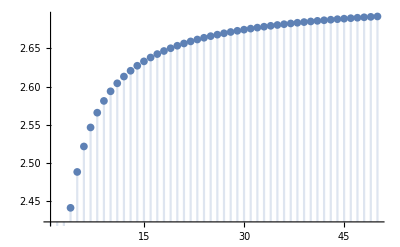

```mathematica
DiscretePlot[a[n], {n, 1, 50}]
```

Así se calcula el límite:

```mathematica
Limit[a[n], {n, 1, 50}]
```

Limit::lim: Limit specification n is not of the form x -> x0.

Limit::lim: Limit specification 1 is not of the form x -> x0.

Limit::lim: Limit specification 50 is not of the form x -> x0.

General::stop: Further output of Limit :: lim will be suppressed during this calculation.

{Limit[((1+n)/n)^n,n],Limit[((1+n)/n)^n,1],Limit[((1+n)/n)^n,50]}

```mathematica
Limit[a[n], n -> Infinity]
```

ⅇ

Podemos ver que esta sucesión se va acercando al número e en la tabla y la matriz. Pero lo hace de una forma muy lenta, por lo que hay que buscar una forma de acelerar la convergencia.

Esta sucesión se acerca al número de oro. Se acerca de forma rápida, tiene una convergencia cuadrática (“los errores disminuyen al cuadrado”).

```mathematica
b[n_] := (2/b[n-1]+b[n-1])/2
```

```mathematica
b[1] = 1
```

1

```mathematica
MatrixForm[N[Table[{b[n], Sqrt[2]}, {n, 1, 20}],10]]
```

(1. | 1.414213562
1.5 | 1.414213562
1.416666667 | 1.414213562
1.414215686 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562
1.414213562 | 1.414213562)